## Bidirectional Mother Machine

```mathematica
ClearAll["Global'*"]
Names["Global'*"]
```

{}

### Probability of fixation

#### We separate our space into N ‘chunks’ that do not have to correspond to cells. Suppose our system is separable into 2 regions where each region has one type of cell. We write our master equation for the boundary when it is at the n^th cell: (dP(n,t))/dt=R_+(n-1)P(n-1,t)+R_-(n+1)P(n+1,t)-[R_+(n)+R_-(n)]P(n,t). What are R_+ and R_-? R_+=(∑_(i=0))^n W_+(i) is the sum of all the rates of cells i ≤ n grow to the right and R_-=(∑_(i=n))^N W_-(i) is the sum of rates that cells i > n grow to the left. The rate that a cell grows f(n) is dependent on the position in the channel, but we’re not too sure how... but here’s an approximation for W=W_++W_-: W=f(i)=4r 1/(1+(lo/l)^a)(i/N -1/2)^2+r 1/(1+(l/lo)^a)

```mathematica
params={l->1.,lo-> 10.0,a->1,r->1};
```

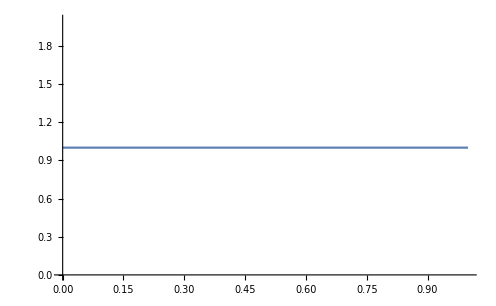

```mathematica
c=1/( 1+(lo/l)^a);
d= 1/( 1+(l/lo)^a);
f[x_]=4 c (x-1/2)^2+d;
f[x_]=r;
Plot[f[x]/.params,{x,0.,1.}]
```

#### Additionally, the rate of growth of a cell is the sum of the rate of growth to the right + rate of growth to the left. As such R=f(n)=R_++R_-=f(n)(n/N+(N-n)/N) W_+(i)=f(i) i/N W_-(i)=f(i) (N-i)/N R_+(n)=(∑_(i=0))^n f(i) i/N R_-(n)=(∑_(i=n))^N f(i) (N-i)/N

#### Now we can expand our master to a FP equation and an equivalent backwards FP: -(∂P(x,t|x_0,t_0))/(∂t)=A(x_0)(∂P)/(∂x_0)+(B(x_0))/2(∂^2 P)/(∂x_0^2)=L_x_0 P For the probability of exiting to the right P_R(x_0) or left P_L(x_0), solve L_x_0 P_R(x_0)=L_x_0 P_R(x_0)=0 with appropriate boundary condition.

```mathematica
A= r (Integrate[f[n]n,{n,0,x}]-Integrate[f[1-n](1-n),{n,x,1}])/.params;
B= r(Integrate[f[n]n,{n,0,x}]+Integrate[f[1-n](1-n),{n,x,1}])/.params;
```

```mathematica
AoverB=A/B;
```

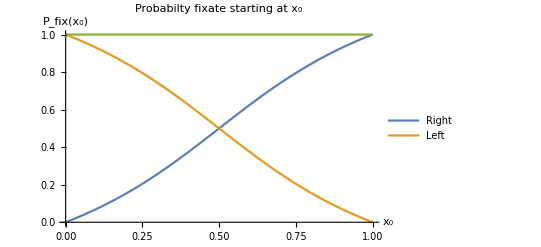

```mathematica
expfg= FullSimplify[Exp[-2 Integrate[AoverB,x]]];
(* Unfortunately, can't seem to integrate this equation, thus need to come up with another scheme to do this... P=Integrate[expfg,x] *)
ProbR[x0_]:=NIntegrate[expfg,{x,0,x0}]/NIntegrate[expfg,{x,0,1}];
ProbL[x0_]:=NIntegrate[expfg,{x,x0,1}]/NIntegrate[expfg,{x,0,1}];
Plot[{ProbR[x],ProbL[x],ProbR[x]+ProbL[x]},{x,0,1},PlotLabel->"Probabilty fixate starting at x_0",PlotLegends->{"Right","Left"},AxesLabel->{"x_0","P_fix(x_0)"}]
```

### Mean time to fixation

#### Stochastic L_x_0<t(x_0)> =-1

```mathematica
a=0.;
b=1.;
```

```mathematica
phi1=Exp[2 Integrate[ AoverB,x]-(2 Integrate[ AoverB,x]/.x->a)];
phi2[y1_?NumericQ]:=phi2[y1]=2 NIntegrate[ phi1/B,{x,a,y1}];
```

```mathematica
phi3[y2_?NumericQ]:=phi3[y2]=NIntegrate[1/phi1,{x,a,y2}];
phi4[y3_?NumericQ]:=phi4[y3]=NIntegrate[phi2[x]/phi1,{x,a,y3}];
MFPT[x0_]:=(phi3[x0]phi4[b]-phi3[b]phi4[x])/phi3[b]
```

#### Deterministic dx/dt=R(x)x, where R(x)=(∫_0.5)^x f(y)dy|

```mathematica
detgrowth=Integrate[1/((Integrate[f[x],x])-(Integrate[f[y],y]/.{y->0.5 }))x,x]/.params
timegrowth[y_]=Re[((detgrowth/.{x-> l/2.})-(detgrowth/.{x-> l Sqrt[(y- 0.5)^2]}))/.params];
detgrowth/.{x-> 0.5}
timegrowth[0.4]
```

x+0.5 Log[0.5-1. x]

Indeterminate

Indeterminate

#### Plots

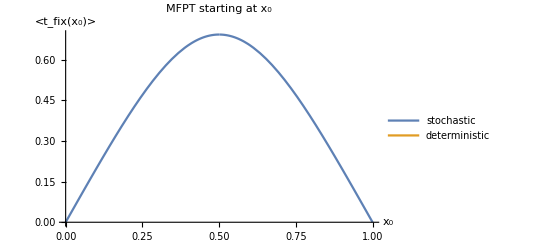

```mathematica
Plot[{MFPT[x],timegrowth[x]},{x,0.,1.},Exclusions->x==0.5,PlotLabel->"MFPT starting at x_0",PlotLegends->{"stochastic","deterministic"},AxesLabel->{"x_0","<t_fix(x_0)>"}]
```

3

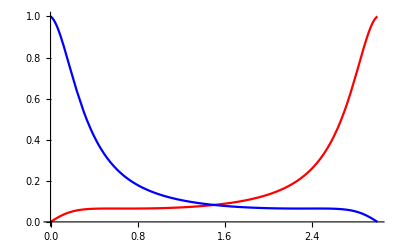

```mathematica
a=3
p1 = Plot[x/(a(1+1(x (a-x))^2)),{x,0,a},PlotRange-> {{0,a},{0,1}},PlotStyle-> Red];
p2 = Plot[(a-x)/(a(1+1(x (a-x))^2)),{x,0,a},PlotRange-> {{0,a},{0,1}},PlotStyle-> Blue];
Show[p1,p2]
```

```mathematica
AAA= FullSimplify[Integrate[x/(1+1/l^4( x(1-x))^2),{x,0,m},Assumptions-> l>0]];(*,PrincipalValue->True*)
```

$Aborted

```mathematica
FullSimplify[ToRadicals@Normal[AAA]]
AAA/.l-> 1.0
```

-1/4 ⅈ ((3.33067×10^-16+6.54874 ⅈ)-(1.38817+0.303078 ⅈ) Log[(-2.60049+1.24962 ⅈ)+2 m]-(0.611825-0.303078 ⅈ) Log[(0.600485-1.24962 ⅈ)+2 m]+(0.388175-0.303078 ⅈ) ((2.60049+1.24962 ⅈ) Log[(-2.60049-1.24962 ⅈ)+2 m]+(0.600485+1.24962 ⅈ) Log[(0.600485+1.24962 ⅈ)+2 m]))

```mathematica
L=10; a=4;
FullSimplify[(AAA/.{l-> L,x-> L-a})-(AAA/.{l-> L,x-> a})](*,Assumptions-> {l>0}]*)
(* FullSimplify[(AAA-BBB)/.{z-> l-x}/.{l-> L,x-> a}],Assumptions-> {l>0}]*)
```

1/1252 5 (-(626 ArcTan[Im[√(25-ⅈ)]/(-1+Re[√(25-ⅈ)])])/(√(25-ⅈ))+√(15650+626 ⅈ) ArcTan[Im[√(25-ⅈ)]/(1+Re[√(25-ⅈ)])]+(626 ArcTan[Im[√(25+ⅈ)]/(-1+Re[√(25+ⅈ)])])/(√(25+ⅈ))-(626 ArcTan[Im[√(25+ⅈ)]/(1+Re[√(25+ⅈ)])])/(√(25+ⅈ))+(1-25 ⅈ) √(25-ⅈ) ArcTanh[(2 Re[√(25-ⅈ)])/(1+√626)]+(1+25 ⅈ) √(25+ⅈ) ArcTanh[(2 Re[√(25+ⅈ)])/(1+√626)])

```mathematica
Evaluate[1/1252 5 (-(626 ArcTan[Im[√(25-ⅈ)]/(-1+Re[√(25-ⅈ)])])/(√(25-ⅈ))+√(15650+626 ⅈ) ArcTan[Im[√(25-ⅈ)]/(1+Re[√(25-ⅈ)])]+(626 ArcTan[Im[√(25+ⅈ)]/(-1+Re[√(25+ⅈ)])])/(√(25+ⅈ))-(626 ArcTan[Im[√(25+ⅈ)]/(1+Re[√(25+ⅈ)])])/(√(25+ⅈ))+(1-25 ⅈ) √(25-ⅈ) ArcTanh[(2 Re[√(25-ⅈ)])/(1+√626)]+(1+25 ⅈ) √(25+ⅈ) ArcTanh[(2 Re[√(25+ⅈ)])/(1+√626)])]
```

1/1252 5 (-(626 ArcTan[Im[√(25-ⅈ)]/(-1+Re[√(25-ⅈ)])])/(√(25-ⅈ))+√(15650+626 ⅈ) ArcTan[Im[√(25-ⅈ)]/(1+Re[√(25-ⅈ)])]+(626 ArcTan[Im[√(25+ⅈ)]/(-1+Re[√(25+ⅈ)])])/(√(25+ⅈ))-(626 ArcTan[Im[√(25+ⅈ)]/(1+Re[√(25+ⅈ)])])/(√(25+ⅈ))+(1-25 ⅈ) √(25-ⅈ) ArcTanh[(2 Re[√(25-ⅈ)])/(1+√626)]+(1+25 ⅈ) √(25+ⅈ) ArcTanh[(2 Re[√(25+ⅈ)])/(1+√626)])

```mathematica
Solve[1+b(x (l-x))^2==0,x]
```

{{x→1/2 (l-√(-(4 ⅈ)/(√b)+l^2))},{x→1/2 (l+√(-(4 ⅈ)/(√b)+l^2))},{x→1/2 (l-√((4 ⅈ)/(√b)+l^2))},{x→1/2 (l+√((4 ⅈ)/(√b)+l^2))}}

```mathematica
Sqrt[626.]
25.02*25.02
```

25.02

626.